# Retrieving baidu index data

## Demo

### Import figures

```mathematica
cz=Import["D:/qinjie/figure/2011_china_zhian.png"];
sz=Import["D:/qinjie/figure/2011_shenzhen_zhian.png"];
```

### Function P for data retrieving

```mathematica
P[baiduImage_,maxX_,maxY_]:=Module[
{wantedImage,x,y,dummyCodingList,codedImage,ps,ps2,ps3},
wantedImage=ImageTake[baiduImage,{26,221},{6,471}];
x=ImageDimensions[wantedImage][[1]];
y=ImageDimensions[wantedImage][[2]];
dummyCodingList[list_]:=If[#[[1]]>0.90&&0.6<#[[2]]<1&&0<#[[3]]<0.7,1,0]&/@list;
codedImage=dummyCodingList/@ImageData[wantedImage];
ps=Sort[Reverse/@Position[codedImage,1]];
ps2=Mean/@GatherBy[ps,#[[1]]&]//N;
ps3=Transpose[{Round[maxX*ps2[[All,1]]/x],maxY*(y-ps2[[All,2]])/y}];
ListPlot[ps3,AxesOrigin->{0,0},PlotRange->{{0,maxX},{0,maxY}},AxesLabel->{"Days","Activity"},PlotStyle->Orange,Joined->True]
]
```

### retrive data

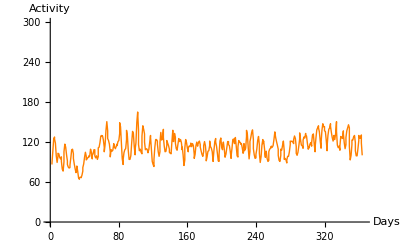

```mathematica
GraphicsGrid[{{cz,P[cz,365,300]}},ImageSize->800]
```

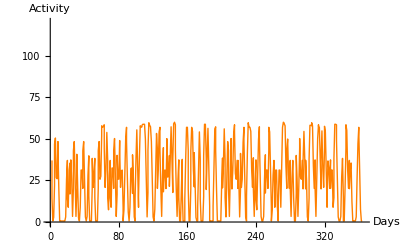

```mathematica
GraphicsGrid[{{sz,P[sz,365,120]}},ImageSize->800]
```

## Guidance: two simple steps to retrieve data from baidu, have a try !

### Download the JPG figures and save as: "D:/qinjie/figure/title.jpg" ;

### Fill the three parameters of function S and click the gray botton ;

```mathematica
1. modify the address like this             D:/github/mathematicar/baidu
2. input infor here:        S["2011_china_qiangjie",365,1200]]
```

## Working platform

```mathematica
S[title_,maxX_,maxY_]:=Module[
{importAdress,baiduImage,wantedImage,x,y,dummyCodingList,codedImage,exportAddress,ps,ps2,ps3},
importAdress="D:/github/mathematicar/baidu/figure/"<>title<>".png";
baiduImage=Import[importAdress];
wantedImage=ImageTake[baiduImage,{26,221},{6,471}];
x=ImageDimensions[wantedImage][[1]];
y=ImageDimensions[wantedImage][[2]];
dummyCodingList[list_]:=If[#[[1]]>0.90&&0.6<#[[2]]<1&&0<#[[3]]<0.7,1,0]&/@list;
codedImage=dummyCodingList/@ImageData[wantedImage];
ps=Sort[Reverse/@Position[codedImage,1]];
ps2=Mean/@GatherBy[ps,#[[1]]&]//N;
ps3=Transpose[{Round[maxX*ps2[[All,1]]/x],maxY*(y-ps2[[All,2]])/y}];
exportAddress="D:/github/mathematicar/baidu/data/"<>title<>".csv";
Export[exportAddress,ps3]
]
```

```mathematica
Button[" click here to run S ",S["2011_china_qiangjie",365,1200]]
```

click here to run S